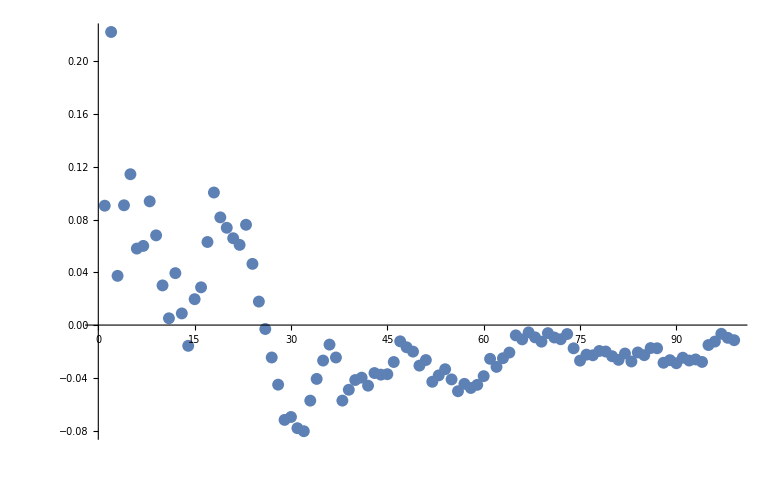

```mathematica
(* Sample Mean of a Levy and of a Normal Distribution *)
NN=100;
dataR=RandomVariate[NormalDistribution[0,0.5],NN];
dataRc=Table[Drop[dataR,-1*n],{n,1,NN-1}];
sum1={};
For[j=1,j≤ NN-1,j++,AppendTo[sum1,Mean[dataRc[[NN-j]]]//N   ]];

ListPlot[sum1]
```

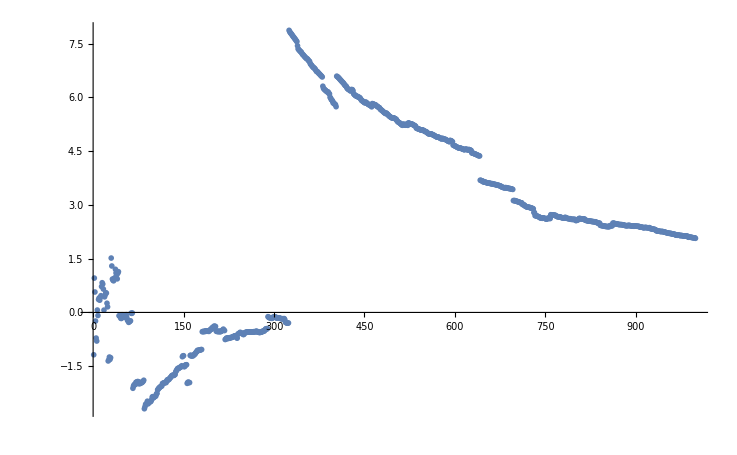

```mathematica
NN=1000;
dataS=RandomVariate[StableDistribution[1,1,0,0,1.5],NN];
dataSc=Table[Drop[dataS,-1*n],{n,1,NN-1}];
sum2={};
For[j=1,j≤ NN-1,j++,AppendTo[sum2,Mean[dataSc[[NN-j]]]//N   ]];

ListPlot[sum2]
```